# M-th photon emission probability

## Enter subtitle here

Enter subsubtitle here

Vladislav Bushmakin

PI 3, Uni Stuttgart

10.10.2020

1. Kosugi, N., Matsuo, S., Konno, K. & Hatakenaka, N. Theory of damped Rabi oscillations. Phys. Rev. B - Condens. Matter Mater. Phys. 72, 2–5 (2005).

```mathematica
P[τ_] :=1/2*(A*Exp[-a* τ]+ C*Exp[-c* τ]*Sin[Ω*τ + Θ]);
ns = 10^-9;
MHz = 10^6;
η = 0;
Γ1 =  1/(10ns);
Γ0 =  0;
Subscript[γ, 10] = 0;
Subscript[γ, ϕ]= 1/(20 ns);
Γp=Γ1+Γ0;
Γ = 1/2(Γ1+Γ0+ Subscript[γ, 10]) + Subscript[γ, ϕ];
Subscript[a, 1]= 1/2 Γp;
Subscript[c, 1] = 1/4(2Γ + (Γp + 2 Subscript[γ, 10]));
```

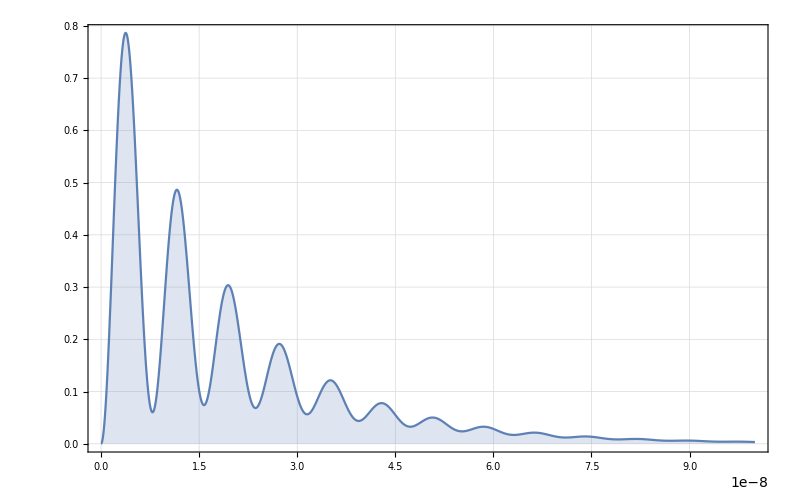

```mathematica
varParams1 = {A -> 1,Ω-> 800 MHz,a -> Subscript[a, 1],C -> 1,c->Subscript[c, 1], Θ -> -1.6};
plt1 = Plot[{P[τ] /. varParams1}, {τ,0,100 ns},PlotRange-> All,Frame-> True,GridLines-> Automatic,ImageSize-> 800,PlotPoints->100, Filling->0]
```

```mathematica
Pnorm1 = Integrate[P[τ],{τ, 0, ∞}];
P2a =Integrate[P[t]*P[τ - t], {t, 0, τ}];
P2at[τ_] =P2a;
```

```mathematica
P3a =Integrate[P2at[t]*P[τ - t], {t, 0, τ}];
P3at[τ_] =P3a;
```

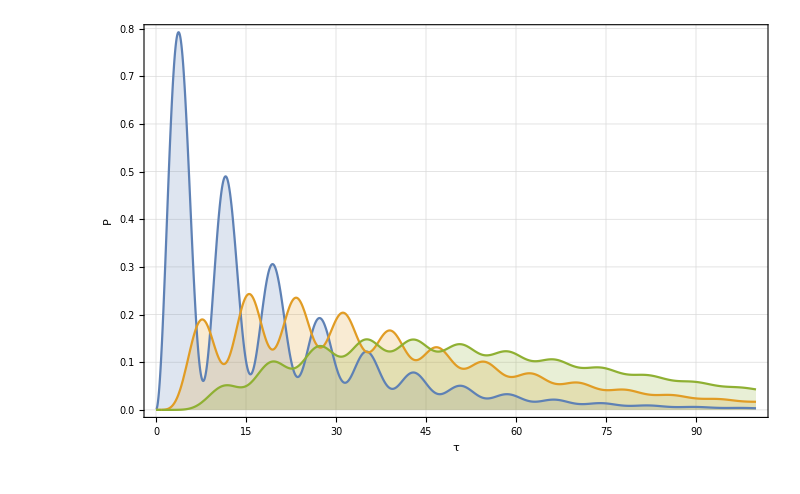

m-thPhoton.pdf

```mathematica
varParams1 = {A -> 1,Ω-> 800 MHz,a -> Subscript[a, 1],C -> 1,c->Subscript[c, 1], Θ -> -1.6};
plt1 = Plot[{{P[τ*ns]/(10^8 Pnorm1) /. varParams1},{P2at[τ*ns]/(10^8 Pnorm1^2)/. varParams1},{P3at[τ*ns]/(10^8 Pnorm1^3) /. varParams1}}, {τ,0,100},PlotRange-> All,Frame-> True,GridLines-> Automatic,ImageSize-> 800,PlotPoints->100, Filling->0,LabelStyle->(FontSize->25), Axes-> Ture, AxesLabel->{τ, P}]
(*Export["m-thPhoton.pdf",plt1];*)
```